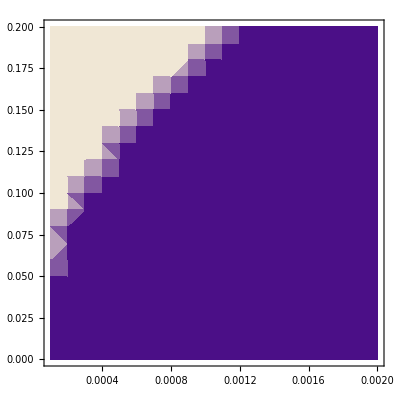

```mathematica
Σ[λ_,m_]:=N[1/2(1/(λ+m)+1/(4+λ+m))];
Ptot[c_,λ_,m_]:=(2 λ Σ[λ])/c(√(c+1)+1)+c/(m+λ)Max[Abs[4+m],Abs[m]];
minPtot[λ_,m_]:=Module[{FF,α,β},
α=N[2λ Σ[λ,m]]; β=N[Max[Abs[4+m],Abs[m]]/(m+λ)];
FF=FindMinimum[{α/c(√(c+1)+1)+β  c,c>0},{c,1.0}];
FF[[1]]
];
M=Table[
mp=minPtot[λ,m];
If[mp<1,{λ,m,1},{λ,m,0}]
,{λ,0.0001,0.002,0.0001},{m,0.0,0.2,0.01}];
M=Flatten[M,1];
ListDensityPlot[M]
```

```mathematica
ListDensityPlot[M]
```

-Graphics-